```mathematica
loadTable[path_]:= Import[NotebookDirectory[]<>path, "Table"]
totalColumn[raw_, colNum_]:= Total[Transpose[Drop[raw, 1]][[colNum]]]
allTotalColumns[rawList_, colNum_]:= Function[x, totalColumn[x, colNum]]/@ rawList
plotRunTimes[rawList_, varList_, predictorLabel_]:=(
searchTime = Transpose[{varList, allTotalColumns[rawList, 2]}];
veriTime = Transpose[{varList, allTotalColumns[rawList, 7]}];
totalRuntime = Transpose[{varList, allTotalColumns[rawList, 9]}];
(*referenceFunc = Transpose[{varList, Function[x, 60*x^2.4+500000000] /@varList}];*)
ListLogPlot[{searchTime, veriTime, totalRuntime},  PlotRange->Full, Joined->True, Filling-> None, InterpolationOrder->1, PlotLegends->Placed[{"Search Step", "Verification Step", "Total"}, Above], AxesLabel->{predictorLabel, "runtime (ns)"}, ImageSize->Medium]
)
largestFilterBlockLength[raw_]:=Max[Transpose[Drop[raw, 1]][[1]]]
filterTime[raw_, blockLen_]:=(
pos = Position[Transpose[raw][[1]], blockLen];
If[pos=={} , 0,(raw[[pos[[1]]]])[[1]][[9]]]
)
filterTimeRatio[raw_, blockLen_]:=(
t = filterTime[raw, blockLen];
tot = totalColumn[raw, 9];
 t /tot
)
filterLine[rawList_, varList_, blockLen_]:= 
(
y = Function[x, filterTimeRatio[x, blockLen]] /@ rawList;
Transpose[{varList, y}]
)
plotFilterRatios[rawList_, varList_, predictorLabel_]:=
(
smallestFilter = 2;
largestFilter = Max[largestFilterBlockLength /@ rawList];
filterRange = Range[smallestFilter, largestFilter];
allLines =  Function[x, filterLine[rawList, varList, x]] /@ filterRange;
ListLinePlot[allLines,  PlotRange->Full, InterpolationOrder->1, PlotLegends->Placed[filterRange, Above], AxesLabel-> {predictorLabel, "proportion of\ntotal runtime"}, ImageSize->Medium]
)
bothPlots[pathsList_, varList_, predictorLabel_]:=
Module[{raws},
raws = loadTable/@ pathsList;
plotRunTimes[raws, varList,predictorLabel]
plotFilterRatios[raws, varList, predictorLabel]
]
```

```mathematica
raw = loadTable["/outputs/5VM_real.p1.40000.out"];
TableForm[raw]
dropped = Drop[raw, 1];
trans = Transpose[dropped];
cols = trans[[2;;4]];
ready = Transpose[cols];


BarChart[ready, ChartLayout->"Stacked", ChartLabels->{Placed[trans[[1]],Axis],None}, PlotLabel->"Run times for filter-lengths\nfor coverage experiment {5VM_real.p1.40000}", ImageSize->Medium, ChartLegends->Placed[{"search", "verification: successes", "verification: failures"}, Below], AxesLabel->{"filter block\nlength", "runtime\ncontribution (ns)"}]

ListLinePlot[trans[[10]],Filling->Axis, DataRange->{trans[[1]][[1]], trans[[1]][[-1]]}, PlotRange->{0,1}, PlotLabel->"Ratio of time spent searching", ImageSize->Medium, AxesLabel->{"filter block\nlength", "runtime\nproportion"}]
ListLogPlot[{trans[[5]], trans[[6]]},Filling->Axis, DataRange->{trans[[1]][[1]], trans[[1]][[-1]]}, PlotLabel->"Solution count", Joined->True, PlotLegends->Placed[{"Solutions", "Spurious Candidates"}, Below], ImageSize->Medium, AxesLabel->{"filter block\nlength", "solution\ncount"}]


plotRunTimes[]
```

search_blocks | seach_nanos | veri=true_nanos | veri=false_nanos | sol=true_count | sol=false_count | (veri_time) | (veri=true_nano_ratio) | (total_nanos) | (search_nanos_ratio) | (sol=true_count_ratio)
2 | 252374266436 | 388206130317 | 31655228260 | 1167206 | 171093 | 419861358577 | 0.924606 | 640580396755 | 0.393978 | 0.872156
3 | 943833160120 | 1405731076069 | 161800524372 | 4229140 | 872275 | 1567531600441 | 0.89678 | 2349564236192 | 0.401706 | 0.829013
4 | 1618340189143 | 2303130789476 | 308286361170 | 6931822 | 1647313 | 2611417150646 | 0.881947 | 3921470978623 | 0.412687 | 0.807986
5 | 1713875353055 | 2420226961758 | 292987899170 | 7284046 | 1571320 | 2713214860928 | 0.892015 | 4134102314818 | 0.41457 | 0.822557
6 | 976832484711 | 1357124582225 | 167713020356 | 4075384 | 895755 | 1524837602581 | 0.890013 | 2333957066942 | 0.418531 | 0.819809

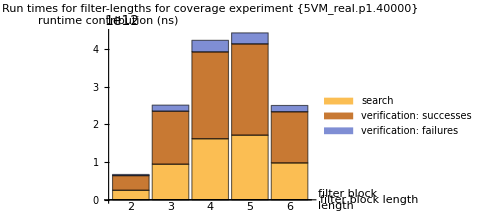
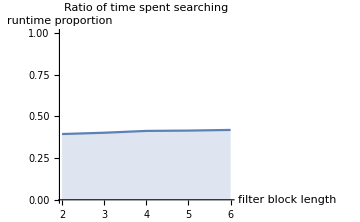
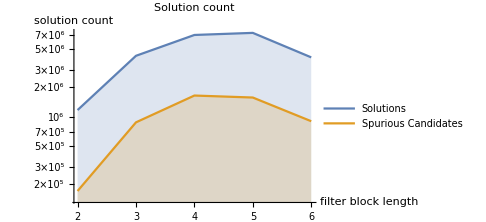

plotRunTimes[]

plotRunTimes[]

```mathematica
gnmlenVars = {5000, 10000, 20000, 50000};
gnmlenPaths = {
"/outputs/reads.5000.out",
"/outputs/reads.10000.out",
"/outputs/reads.20000.out",
"/outputs/reads.50000.out"
};
rdlenVars = {100, 150, 200, 250};
rdlenPaths = {
"/outputs/hxb2.l100.reads.out",
"/outputs/hxb2.l150.reads.out",
"/outputs/hxb2.l200.reads.out",
"/outputs/hxb2.l250.reads.out"
};
covVars = {400, 800, 2000, 4000, 8000, 20000, 40000};
covPaths = {
"/outputs/5VM_real.p1.400.out",
"/outputs/5VM_real.p1.800.out",
"/outputs/5VM_real.p1.2000.out",
"/outputs/5VM_real.p1.4000.out",
"/outputs/5VM_real.p1.8000.out",
"/outputs/5VM_real.p1.20000.out",
"/outputs/5VM_real.p1.40000.out"
};
divVars = { 0.005, 0.01, 0.02, 0.04, 0.08};
divPaths = {
"/outputs/mut0.005.out",
"/outputs/mut0.01.out",
"/outputs/mut0.02.out",
"/outputs/mut0.04.out",
"/outputs/mut0.08.out"
};

bothPlots[gnmPaths, gnmlenVars, "genome length"]
bothPlots[rdlenPaths, rdlenVars, "read length"]
bothPlots[covPaths, covVars, "coverage"]
bothPlots[divPaths, divVars, "divergence"]
```

bothPlots[gnmPaths,{5000,10000,20000,50000},genome length]

bothPlots[{/outputs/hxb2.l100.reads.out,/outputs/hxb2.l150.reads.out,/outputs/hxb2.l200.reads.out,/outputs/hxb2.l250.reads.out},{100,150,200,250},read length]

bothPlots[{/outputs/5VM_real.p1.400.out,/outputs/5VM_real.p1.800.out,/outputs/5VM_real.p1.2000.out,/outputs/5VM_real.p1.4000.out,/outputs/5VM_real.p1.8000.out,/outputs/5VM_real.p1.20000.out,/outputs/5VM_real.p1.40000.out},{400,800,2000,4000,8000,20000,40000},coverage]

bothPlots[{/outputs/mut0.005.out,/outputs/mut0.01.out,/outputs/mut0.02.out,/outputs/mut0.04.out,/outputs/mut0.08.out},{0.005,0.01,0.02,0.04,0.08},divergence]